# Characterization of Selected Bivariate Distributions

## Definition of probability density functions

```mathematica
(*Define the values ​​of the parameters a,b,c,d*){aVal,bVal,cVal,dVal}={3,6,3,6};
(*Define the values ​​of the parameters a,b,c,d*){aVal2,bVal2,cVal2,dVal2}={0.8,6,3,0.2};
```

## Combination 1 (Beta for X_1 and Beta 4P for X_2 | X_1)

```mathematica
f[x_,y_,a_,b_,c_,d_]:= 1/(Beta[a,b]Beta[c,d])(x^(a-1)y^(b-1)(x+y)^(d-(a+b)))/(x+y+1)^(c+d);
fx[x_]:= N[NIntegrate[f[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity}],3];
fy[y_]:= N[NIntegrate[f[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity}],3];
Fx[t_]:= N[NIntegrate[f[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,t}],3];
Fy[t_]:= N[NIntegrate[f[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity},{y,0,t}],3]; 
Plot3df=Plot3D[f[x,y,aVal,bVal,cVal,dVal],{x,0,1},{y,0,3},PlotRange->{0,2},AxesLabel->{Subscript[y, 1],Subscript[y, 2],Density},ColorFunction->"Rainbow",Boxed->False, PlotLabel->"Combination 1"]
```

-Graphics3D-

## Combination 6 (Kumaraswamy for X_1 and Beta 4P for X_2 | X_1)

```mathematica
g[x_,y_,a_,b_,c_,d_]:= (a b)/Beta[c,d](x^(a-1)((x+y)^a-x^a)^(b-1))/((x+y)^(a b-d+1)(x+y+1)^(c+d));
gx[x_]:= N[NIntegrate[g[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity}],3];
gy[y_]:= N[NIntegrate[g[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity}],3];
Gx[t_]:=  N[NIntegrate[g[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,t}],3];
Gy[t_]:= N[NIntegrate[g[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity},{y,0,t}],3];
Plot3dg=Plot3D[g[x,y,aVal,bVal,cVal,dVal],{x,0,1},{y,0,3},PlotRange->{0,2},AxesLabel->{Subscript[y, 1],Subscript[y, 2],Density},ColorFunction->"Rainbow",Boxed->False, PlotLabel->"Combination 6"]
```

-Graphics3D-

## Combination 8 (Kumaraswamy for X_1 and Triangular for X_2| X_1)

```mathematica
h[x_,y_,a_,b_,d_]:= (2 a b)/d (x^(a-1)((x+y)^a-x^a)^(b-1))/((x+y)^(a b)(x+y+1)^2)  Which[0<=x y<d(x+y)^2(x+y+1),(x y)/((x+y)^2(x+y+1)),x y==d(x+y)^2(x+y+1),d ,d(x+y)^2<d(x+y)^2(x+y+1)<=x y,(x y(x+y) d)/((x+y+1)(x y-d(x+y)^2))];
hx[x_]:= N[NIntegrate[h[x,y,a=aVal,b=bVal2,d=dVal2],{y,0,Infinity},Method->"Oscillatory"],3];hy[y_]:= N[NIntegrate[h[x,y,a=aVal,b=bVal2,d=dVal2],{x,0,Infinity},Method->"Oscillatory"],3];
Hx[t_]:=  N[NIntegrate[h[x,y,a=aVal,b=bVal2,d=dVal2],{y,0,Infinity},{x,0,t},AccuracyGoal->4,PrecisionGoal->4],3];
Hy[t_]:=  N[NIntegrate[h[x,y,a=aVal,b=bVal2,d=dVal2],{x,0,Infinity},{y,0,t},AccuracyGoal->4,PrecisionGoal->4],3];
Plot3dh=Plot3D[h[x,y,aVal,bVal2,dVal2],{x,0,1},{y,0,3},PlotRange->{0,2},AxesLabel->{Subscript[y, 1],Subscript[y, 2],Density},ColorFunction->"Rainbow",Boxed->False, PlotLabel->"Combination 8"]
```

-Graphics3D-

## Combination 11 (Triangular for X_1 and Beta 4P for X_2| X_1)

```mathematica
j[x_,y_,a_,c_,d_]:=  2/(a Beta[c,d]) (x+y)^(d-2)/(x+y+1)^(c+d)Which[0<=x <a(x+y),x/(x+y),x==y/(1-a),a ,a(x+y)<x<=x+y,(y a)/((1-a)(x+y))];
jx[x_]:= N[NIntegrate[j[x,y,a=aVal2,c=cVal2,d=dVal2],{y,0,Infinity}],3];
jy[y_]:= N[NIntegrate[j[x,y,a=aVal2,c=cVal2,d=dVal2],{x,0,Infinity}],3];
Jx[t_]:=  N[NIntegrate[j[x,y,a=aVal2,c=cVal2,d=dVal2],{y,0,Infinity},{x,0,t}],3];
Jy[t_]:= N[NIntegrate[j[x,y,a=aVal2,c=cVal2,d=dVal2],{x,0,Infinity},{y,0,t}],3];
Plot3dj=Plot3D[j[x,y,aVal2,cVal2,dVal2],{x,0,1},{y,0,3},PlotRange->{0,2},AxesLabel->{Subscript[y, 1],Subscript[y, 2],Density},ColorFunction->"Rainbow",Boxed->False, PlotLabel->"Combination 11"]
```

-Graphics3D-

## Combination 14 (Triangular for X_1 and Truncated Gamma for X_2 | X_1)

```mathematica
k[x_,y_,a_,c_,d_]:= 2/(a d^c)(x^c y^c)/((x+y)^(2 c+1)(x+y+1)^(c+1)) Which[0<=x <a(x+y),x/(x+y),x (1-a)==y,a ,a(x+y)<x<=x+y,(y a)/((1-a)(x+y))] Exp[-(x y)/(d (x+y)^2(x+y+1))]/Gamma[c,0,(x y)/(d(x+y)^2)];
kx[x_]:= N[NIntegrate[k[x,y,a=aVal2,c=cVal2,d=dVal2],{y,0,Infinity}],3];
ky[y_]:= N[NIntegrate[k[x,y,a=aVal2,c=cVal2,d=dVal2],{x,0,Infinity}],3];
Kx[t_]:=  N[NIntegrate[k[x,y,a=aVal2,c=cVal2,d=dVal2],{y,0,Infinity},{x,0,t}],3];
Ky[t_]:= N[NIntegrate[k[x,y,a=aVal2,c=cVal2,d=dVal2],{x,0,Infinity},{y,0,t}],3];
Plot3dk=Plot3D[k[x,y,aVal2,cVal2,dVal2],{x,0,1},{y,0,3},PlotRange->{0,2},AxesLabel->{Subscript[y, 1],Subscript[y, 2],Density},ColorFunction->"Rainbow",Boxed->False, PlotLabel->"Combination 14"]
```

-Graphics3D-

## Combination 19 (Truncated Gamma for X_1 y Truncated Gamma for X_2 | X_1)

```mathematica
l[x_,y_,a_,b_,c_,d_]:= 1/(b^a d^c(Gamma[a,0,1/b]))(x^(a+c-1) y^c)/((x+y)^(a+2 c)(x+y+1)^(c+1)) Exp[-(x y)/(d (x+y)^2(x+y+1))-x/(b(x+y))]/Gamma[c,0,(x y)/(d(x+y)^2)];
lx[x_]:= N[NIntegrate[l[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity}],3];
ly[y_]:= N[NIntegrate[l[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity}],3];
Lx[t_]:=  N[NIntegrate[l[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,t}],3];
Ly[t_]:= N[NIntegrate[l[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity},{y,0,t}],3];
Plot3dl=Plot3D[l[x,y,aVal,bVal,cVal,dVal],{x,0,1},{y,0,3},PlotRange->{0,2},AxesLabel->{Subscript[y, 1],Subscript[y, 2],Density},ColorFunction->"Rainbow",Boxed->False, PlotLabel->"Combination 19"]
```

-Graphics3D-

## Combination 25 (Truncated Normal for X_1 and Truncated Normal for X_2 | X_1)

```mathematica
e[x_,y_,a_,b_,c_,d_]:= 1/(( CDF[NormalDistribution[0,1],(1-a)/Sqrt[b]]-CDF[NormalDistribution[0,1],-a/Sqrt[b]]) 2Pi Sqrt[ b d])(x y)/((x+y)^3(x+y+1)^2)Exp[-1/(2d)((x y)/((x+y)^2(x+y+1))-c)^2-1/(2*b)(x/(x+y)-a)^2]/(CDF[NormalDistribution[0,1],((x y)/(x+y)^2-c)/Sqrt[d]]-CDF[NormalDistribution[0,1],-c/Sqrt[d]]);
ex[x_]:= N[NIntegrate[e[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity}],3];
ey[y_]:= N[NIntegrate[e[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity}],3];
Ex[t_]:=  N[NIntegrate[e[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,t}],3];
Ey[t_]:= N[NIntegrate[e[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity},{y,0,t}],3];
Plot3de=Plot3D[e[x,y,aVal,bVal,cVal,dVal],{x,0,1},{y,0,3},PlotRange->{0,2},AxesLabel->{Subscript[y, 1],Subscript[y, 2],Density},ColorFunction->"Rainbow",Boxed->False, PlotLabel->"Combination 25"]
```

-Graphics3D-

## Surface

```mathematica
GraphicsGrid[{{Plot3df,Plot3dg},{Plot3dh,Plot3dj},{Plot3dk,Plot3dl},{Plot3de,}}]
```

-Graphics-

## Contour Lines

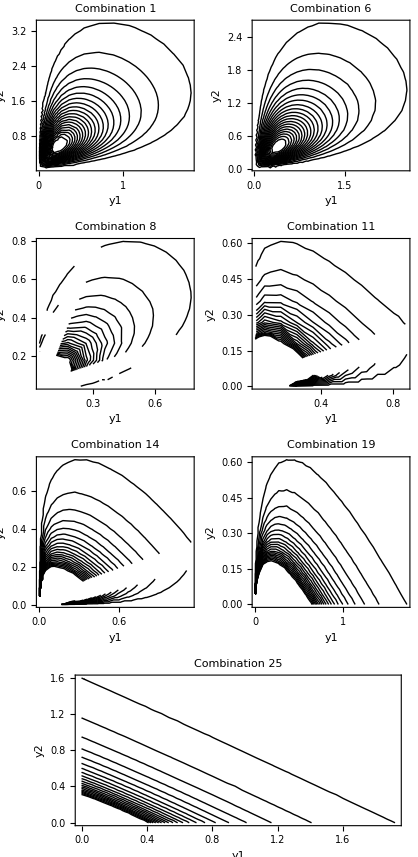

```mathematica
(*Generation of contour lines for the different functions*)
contourPlotF=ContourPlot[f[x,y,aVal,bVal,cVal,dVal],{x,0,10},{y,0,10},Contours->20,ContourShading->None,PlotRange->All,FrameLabel->{"y1","y2"},PlotLabel->"Combination 1"];
contourPlotG=ContourPlot[g[x,y,aVal,bVal,cVal,dVal],{x,0,10},{y,0,10},Contours->20,ContourShading->None,PlotRange->All,FrameLabel->{"y1","y2"},PlotLabel->"Combination 6"];
contourPlotH=ContourPlot[h[x,y,aVal,bVal2,dVal2],{x,0,10},{y,0,10},Contours->20,ContourShading->None,PlotRange->All,FrameLabel->{"y1","y2"},PlotLabel->"Combination 8"];
contourPlotJ=ContourPlot[j[x,y,aVal2,cVal2,dVal2],{x,0,10},{y,0,10},Contours->20,ContourShading->None,PlotRange->All,FrameLabel->{"y1","y2"},PlotLabel->"Combination 11"];
contourPlotK=ContourPlot[k[x,y,aVal2,cVal2,dVal2],{x,0,10},{y,0,10},Contours->20,ContourShading->None,PlotRange->All,FrameLabel->{"y1","y2"},PlotLabel->"Combination 14"];
contourPlotL=ContourPlot[l[x,y,aVal,bVal,cVal,dVal],{x,0,10},{y,0,10},Contours->20,ContourShading->None,PlotRange->All,FrameLabel->{"y1","y2"},PlotLabel->"Combination 19"];
contourPlotD=ContourPlot[e[x,y,aVal,bVal,cVal,dVal],{x,0,10},{y,0,10},Contours->20,ContourShading->None,PlotRange->All,FrameLabel->{"y1","y2"},PlotLabel->"Combination 25"];
(*Show the graphs together*)
GraphicsGrid[{{contourPlotF,contourPlotG},{contourPlotH,contourPlotJ},{contourPlotK,contourPlotL},{contourPlotD,SpanFromLeft}}]
```

## Marginal Density Function

```mathematica
LaunchKernels[7];
DistributeDefinitions[fx,fy,gx,gy,hx,hy,jx,jy,kx,ky,lx,ly,ex,ey];
generatePlotfx:=Module[{pointsx,label},pointsx=ParallelTable[{x,fx[x]},{x,0.1,6,0.1}];
label="Combination 1";
ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotfy:=Module[{pointsy,label},pointsy=ParallelTable[{y,fy[y]},{y,0.1,6,0.1}];
label="Combination 1";ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];
generatePlotgx:=Module[{pointsx,label},pointsx=ParallelTable[{x,gx[x]},{x,0.1,6,0.1}];
label="Combination 6";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotgy:=Module[{pointsy,label},pointsy=ParallelTable[{y,gy[y]},{y,0.1,6,0.1}];
label="Combination 6";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];
generatePlothx:=Module[{pointsx,label},pointsx=ParallelTable[{x,hx[x]},{x,0.1,6,0.1}];
label="Combination 8";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlothy:=Module[{pointsy,label},pointsy=ParallelTable[{y,hy[y]},{y,0.1,6,0.1}];
label="Combination 8";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];
generatePlotjx:=Module[{pointsx,label},pointsx=ParallelTable[{x,jx[x]},{x,0.1,6,0.1}];
label="Combination 11";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotjy:=Module[{pointsy,label},pointsy=ParallelTable[{y,jy[y]},{y,0.1,6,0.1}];
label="Combination 11";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];
generatePlotkx:=Module[{pointsx,label},pointsx=ParallelTable[{x,kx[x]},{x,0.1,6,0.1}];
label="Combination 14";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotky:=Module[{pointsy,label},pointsy=ParallelTable[{y,ky[y]},{y,0.1,6,0.1}];
label="Combination 14";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];
generatePlotlx:=Module[{pointsx,label},pointsx=ParallelTable[{x,lx[x]},{x,0.1,6,0.1}];
label="Combination 19";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotly:=Module[{pointsy,label},pointsy=ParallelTable[{y,ly[y]},{y,0.1,6,0.1}];
label="Combination 19";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];
generatePlotex:=Module[{pointsx,label},pointsx=ParallelTable[{x,ex[x]},{x,0.1,6,0.1}];
label="Combination 25";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotey:=Module[{pointsy,label},pointsy=ParallelTable[{y,ey[y]},{y,0.1,6,0.1}];
label="Combination 25";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];
```

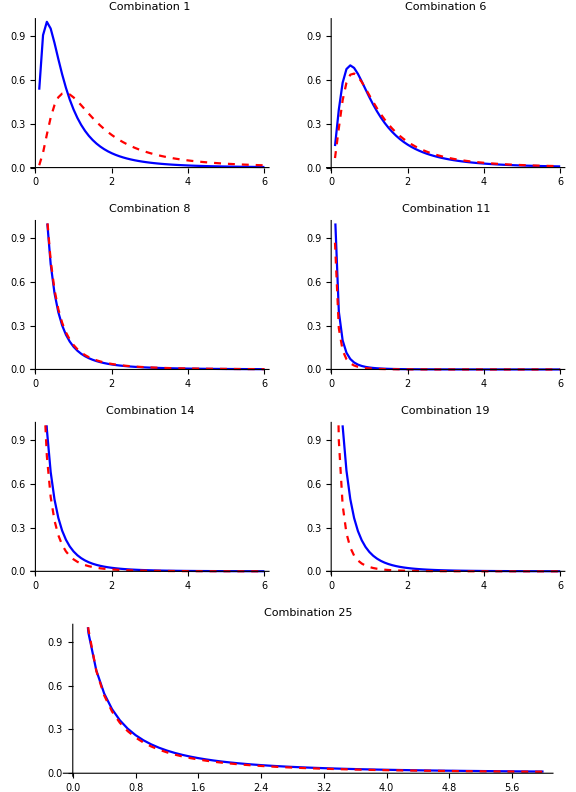

```mathematica
plots = {Show[generatePlotfx, generatePlotfy],Show[generatePlotgx, generatePlotgy],Show[generatePlothx, generatePlothy],Show[generatePlotjx, generatePlotjy],
Show[generatePlotkx, generatePlotky],Show[generatePlotlx, generatePlotly],Show[generatePlotex, generatePlotey],SpanFromLeft};
combinedPlot = GraphicsGrid[Partition[plots, 2], Spacings -> {20, 20}, 
  ImageSize -> Large]
(* Añadir la leyenda *)
Legended[combinedPlot, Placed[{"f(y_1)", "f(y_2)"}, Below]];
CloseKernels[];
```

## Cumulative Probability Distribution

```mathematica
LaunchKernels[7];
DistributeDefinitions[Fx,Fy,Gx,Gy,Hx,Hy,Jx,Jy,Kx,Ky,Lx,Ly,Ex,Ey];
generatePlotFx:=Module[{pointsx,label},pointsx=ParallelTable[{t,Fx[t]},{t,0.1,6,0.1}];
label="Combinación 1";
ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotFy:=Module[{pointsy,label},pointsy=ParallelTable[{t,Fy[t]},{t,0.1,6,0.1}];
label="Combination 1";ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];

generatePlotGx:=Module[{pointsx,label},pointsx=ParallelTable[{t,Gx[t]},{t,0.1,6,0.1}];
label="Combination 6";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotGy:=Module[{pointsy,label},pointsy=ParallelTable[{t,Gy[t]},{t,0.1,6,0.1}];
label="Combination 6";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];

generatePlotHx:=Module[{pointsx,label},pointsx=ParallelTable[{t,Hx[t]},{t,0.1,6,0.1}];
label="Combination 8";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotHy:=Module[{pointsy,label},pointsy=ParallelTable[{t,Hy[t]},{t,0.1,6,0.1}];
label="Combination 8";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];

generatePlotJx:=Module[{pointsx,label},pointsx=ParallelTable[{t,Jx[t]},{t,0.1,6,0.1}];
label="Combination 11";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotJy:=Module[{pointsy,label},pointsy=ParallelTable[{t,Jy[t]},{t,0.1,6,0.1}];
label="Combination 11";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];

generatePlotKx:=Module[{pointsx,label},pointsx=ParallelTable[{t,Kx[t]},{t,0.1,6,0.1}];
label="Combination 14";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotKy:=Module[{pointsy,label},pointsy=ParallelTable[{t,Ky[t]},{t,0.1,6,0.1}];
label="Combination 14";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];

generatePlotLx:=Module[{pointsx,label},pointsx=ParallelTable[{t,Lx[t]},{t,0.1,6,0.1}];
label="Combination 19";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotLy:=Module[{pointsy,label},pointsy=ParallelTable[{t,Ly[t]},{t,0.1,6,0.1}];
label="Combination 19";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];

generatePlotEx:=Module[{pointsx,label},pointsx=ParallelTable[{t,Ex[t]},{t,0.1,6,0.1}];
label="Combination 25";ListPlot[pointsx,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Blue]];
generatePlotEy:=Module[{pointsy,label},pointsy=ParallelTable[{t,Ey[t]},{t,0.1,6,0.1}];
label="Combination 25";
ListPlot[pointsy,Joined->True,PlotRange->{{0,6},{0,1}},PlotLabel->label,PlotStyle->Directive[Red,Dashed]]];
```

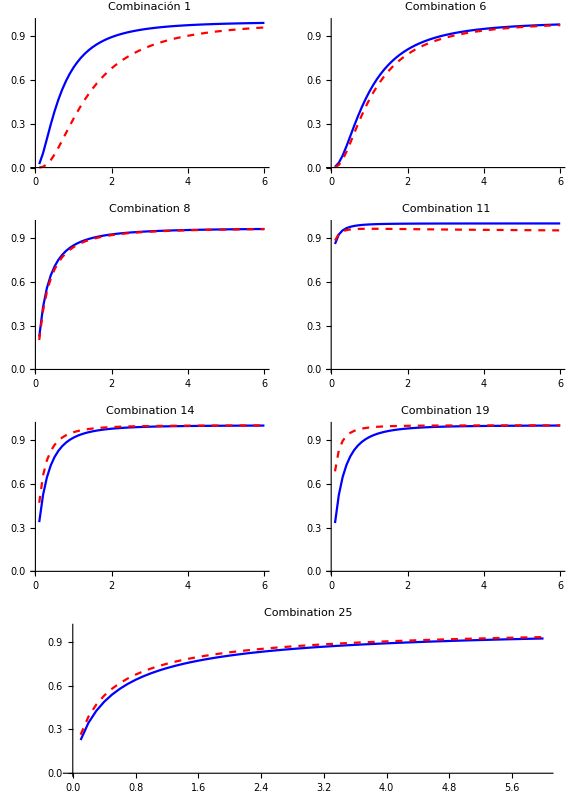

```mathematica
plots = {Show[generatePlotFx, generatePlotFy],Show[generatePlotGx, generatePlotGy],Show[generatePlotHx, generatePlotHy],Show[generatePlotJx, generatePlotJy],
Show[generatePlotKx, generatePlotKy],Show[generatePlotLx, generatePlotLy],Show[generatePlotEx, generatePlotEy],SpanFromLeft};
combinedPlot = GraphicsGrid[Partition[plots, 2], Spacings -> {20, 20}, 
  ImageSize -> Large]
(* Añadir la leyenda *)
Legended[combinedPlot, Placed[{"F(y_1)", "F(y_2)"}, Below]];
CloseKernels[];
```

## Momentos

```mathematica
(*Numerically approximate expected value*)
Efx= NIntegrate[x f[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,Infinity}];
Efy= NIntegrate[y f[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity},{y,0,Infinity}];
Egx= NIntegrate[x g[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,Infinity}];
Egy= NIntegrate[y g[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity},{y,0,Infinity}];
Ehx= NIntegrate[x h[x,y,a=aVal,b=bVal2,d=dVal2],{y,0,Infinity},{x,0,Infinity},AccuracyGoal->4,PrecisionGoal->4];
Ehy= NIntegrate[y h[x,y,a=aVal,b=bVal2,d=dVal2],{x,0,Infinity},{y,0,Infinity},AccuracyGoal->4,PrecisionGoal->4];
Ejx= NIntegrate[x j[x,y,a=aVal2,c=cVal2,d=dVal2],{y,0,Infinity},{x,0,Infinity}];
Ejy= NIntegrate[y j[x,y,a=aVal2,c=cVal2,d=dVal2],{x,0,Infinity},{y,0,Infinity}];
Ekx= NIntegrate[x k[x,y,a=aVal2,c=cVal2,d=dVal2],{y,0,Infinity},{x,0,Infinity}];
Eky= NIntegrate[y k[x,y,a=aVal2,c=cVal2,d=dVal2],{x,0,Infinity},{y,0,Infinity}];
Elx= NIntegrate[x l[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,Infinity},AccuracyGoal->4,PrecisionGoal->4];
Ely= NIntegrate[y l[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity},{y,0,Infinity},AccuracyGoal->4,PrecisionGoal->4];
Eex= NIntegrate[x e[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,Infinity},AccuracyGoal->1,PrecisionGoal->0.1];
Eey= NIntegrate[y e[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity},{y,0,Infinity},AccuracyGoal->1,PrecisionGoal->0.1];
```

```mathematica
(*Reverse transformations from (Subscript[Y, 1],Subscript[Y, 2]) to (Subscript[X, 1],Subscript[X, 2])*)
g1[x_,y_]:=x/(x+y);
g2[x_,y_]:=(x y)/((x+y)^2(x+y+1));
(*Numerical results obtained for the expected values*)
resultadosTabla=TableForm[{{"1",Efx,Efy,g1[Efx,Efy],g2[Efx,Efy]},{"6",Egx,Egy,g1[Egx,Egy],g2[Egx,Egy]},{"8",Ehx,Ehy,g1[Ehx,Ehy],g2[Ehx,Ehy]},{"11",Ejx,Ejy,g1[Ejx,Ejy],g2[Ejx,Ejy]},{"14",Ekx,Eky,g1[Ekx,Eky],g2[Ekx,Eky]},{"19",Elx,Ely,g1[Elx,Ely],g2[Elx,Ely]},{"25",Eex,Eey,g1[Eex,Eey],g2[Eex,Eey]}},TableHeadings->{None,{"Combination","E[Y_1]","E[Y_2]","h_1^-1(Y_1,Y_2)","h_2^-1(Y_1,Y_2)"}} ]
```

Combination | E[Y_1] | E[Y_2] | h_1^-1(Y_1,Y_2) | h_2^-1(Y_1,Y_2)
1 | 1. | 2. | 0.333333 | 0.0555556
6 | 1.423 | 1.577 | 0.474335 | 0.0623353
8 | 0.534093 | 0.575118 | 0.481507 | 0.118366
11 | 0.06 | 0.04 | 0.6 | 0.218182
14 | 0.381234 | 0.260235 | 0.594314 | 0.146884
19 | 0.373937 | 0.129468 | 0.742815 | 0.127072
25 | 3.10711 | 2.65022 | 0.539679 | 0.0367638

```mathematica
(*Expected value Subscript[ofX, 1] Beta distribution*)
EBx1[a_,b_]:=a/(a+b);
(*Expected value of Subscript[X, 2]|Subscript[X, 1] Beta.4P distribution*)
EB4Px2x1[c_,d_,u_]:=(c u)/(c+d);
(*Expected value of Subscript[X, 1] Kumaraswamy distribution*)
EKx1[a_,b_]:=b Beta[1+1/a,b];
(*Expected value of Subscript[X, 2]|Subscript[X, 1] Truncated Kumaraswamy distribution*)
EKTx2x1[c_,d_,u_]:=(c d NIntegrate[x^c (1-x^c)^(d-1),{x,0,u}])/(1-(1-(u)^c)^d);
(*Expected value of Subscript[X, 1] Triangular distribution*)
ETx1[a_]:=(a+1)/3;
(*Expected value of Subscript[X, 2]|Subscript[X, 1] Triangular distribution*)
ETx2x1[d_,u_]:=(d+u)/3;
(*Expected value of Subscript[X, 1] GT distribution*)
EGTx1[a_,b_]:=NIntegrate[x^a Exp[-x/b],{x,0,1}]/NIntegrate[w^(a-1)Exp[-w/b],{w,0,1}];
(*Expected value of Subscript[X, 2]|Subscript[X, 1] GT distribution*)
EGTx2x1[c_,d_,u_]:=NIntegrate[x^c Exp[-x/d],{x,0,u}]/NIntegrate[w^(c-1)Exp[-w/d],{w,0,u}];
(*Expected value of Subscript[X, 1] NT distribution*)
ENTx1[a_,b_]:=NIntegrate[x Exp[-1/(2b)(x -a)^2],{x,0,1}]/(( CDF[NormalDistribution[0,1],(1-a)/Sqrt[b]]-CDF[NormalDistribution[0,1],-a/Sqrt[b]]) Sqrt[2Pi b]);
(*Expected value of Subscript[X, 2]|Subscript[X, 1] NT distribution*)
ENTx2x1[c_,d_,u_]:=NIntegrate[x Exp[-1/(2d)(x -c)^2],{x,0,u}]/(( CDF[NormalDistribution[0,1],(u-c)/Sqrt[d]]-CDF[NormalDistribution[0,1],-c/Sqrt[d]]) Sqrt[2Pi d]);
```

```mathematica
(*Comparison between numerical results obtained and the marginal and conditional expected values*)
resultadosTabla=N[TableForm[{{"1",Efx,Efy,g1[Efx,Efy],g2[Efx,Efy],EBx1[aVal,bVal],EB4Px2x1[cVal,dVal,EBx1[aVal,bVal](1-EBx1[aVal,bVal])]},{"6",Egx,Egy,g1[Egx,Egy],g2[Egx,Egy],EKx1[aVal,bVal],EB4Px2x1[cVal,dVal,EKx1[aVal,bVal](1-EKx1[aVal,bVal])]},{"8",Ehx,Ehy,g1[Ehx,Ehy],g2[Ehx,Ehy],EKx1[aVal,bVal2],ETx2x1[dVal2,EKx1[aVal,bVal2](1-EKx1[aVal,bVal2])]},{"11",Ejx,Ejy,g1[Ejx,Ejy],g2[Ejx,Ejy],ETx1[aVal2],EB4Px2x1[cVal2,dVal2,ETx1[aVal2](1-ETx1[aVal2])]},
{"14",Ekx,Eky,g1[Ekx,Eky],g2[Ekx,Eky],ETx1[aVal2],EGTx2x1[cVal2,dVal2,ETx1[aVal2](1-ETx1[aVal2])]},{"19",Elx,Ely,g1[Elx,Ely],g2[Elx,Ely],EGTx1[aVal,bVal],EGTx2x1[cVal,dVal,EGTx1[aVal,bVal](1-EGTx1[aVal,bVal])]},
{"25",Eex,Eey,g1[Eex,Eey],g2[Eex,Eey],ENTx1[aVal,bVal],ENTx2x1[cVal,dVal,ENTx1[aVal,bVal](1-ENTx1[aVal,bVal])]}},TableHeadings->{None,{"Combination","E[Y_1]","E[Y_2]","h_1^-1(E[Y_1],E[Y_2])","h_2^-1(E[Y_1],E[Y_2])","E[X_1]","E[X_2|X_1=E[X_1]]"}} ],5]
```

Combination | E[Y_1] | E[Y_2] | h_1^-1(E[Y_1],E[Y_2]) | h_2^-1(E[Y_1],E[Y_2]) | E[X_1] | E[X_2|X_1=E[X_1]]
1 | 1. | 2. | 0.333333 | 0.0555556 | 0.33333 | 0.074074
6 | 1.423 | 1.577 | 0.474335 | 0.0623353 | 0.47433 | 0.083114
8 | 0.534093 | 0.575118 | 0.481507 | 0.118366 | 0.47433 | 0.14978
11 | 0.06 | 0.04 | 0.6 | 0.218182 | 0.6 | 0.225
14 | 0.381234 | 0.260235 | 0.594314 | 0.146884 | 0.6 | 0.168126
19 | 0.373937 | 0.129468 | 0.742815 | 0.127072 | 0.743663 | 0.142743
25 | 3.10711 | 2.65022 | 0.539679 | 0.0367638 | 0.534431 | 0.126878

```mathematica
(*Numerically approximated covariance*)
Cf= NIntegrate[x y f[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,Infinity},AccuracyGoal->4,PrecisionGoal->4];
Cg= NIntegrate[x y g[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,Infinity}];
Ch= NIntegrate[x y h[x,y,a=aVal,b=bVal2,d=dVal2],{y,0,Infinity},{x,0,Infinity},AccuracyGoal->1,PrecisionGoal->4];
Cj= NIntegrate[x y j[x,y,a=aVal2,c=cVal2,d=dVal2],{y,0,Infinity},{x,0,Infinity}];
Ck= NIntegrate[x y k[x,y,a=aVal2,c=cVal2,d=dVal2],{y,0,Infinity},{x,0,Infinity}];
Cl= NIntegrate[x y l[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{y,0,Infinity},{x,0,Infinity}];
Ce= NIntegrate[x y e[x,y,a=aVal,b=bVal,c=cVal,d=dVal],{x,0,Infinity},{y,0,Infinity},AccuracyGoal->1,PrecisionGoal->0.1];
```

```mathematica
(*Covariance*)
resultadosTabla=N[TableForm[{{"1",Efx,Efy,g1[Efx,Efy],g2[Efx,Efy],EBx1[aVal,bVal],EB4Px2x1[cVal,dVal,EBx1[aVal,bVal](1-EBx1[aVal,bVal])],Cf,Cf-Efx Efy},{"6",Egx,Egy,g1[Egx,Egy],g2[Egx,Egy],EKx1[aVal,bVal],EB4Px2x1[cVal,dVal,EKx1[aVal,bVal](1-EKx1[aVal,bVal])],Cg,Cg-Egx Egy},{"8",Ehx,Ehy,g1[Ehx,Ehy],g2[Ehx,Ehy],EKx1[aVal,bVal2],ETx2x1[dVal2,EKx1[aVal,bVal2](1-EKx1[aVal,bVal2])],Ch,Ch-Ehx Ehy},{"11",Ejx,Ejy,g1[Ejx,Ejy],g2[Ejx,Ejy],ETx1[aVal2],EB4Px2x1[cVal2,dVal2,ETx1[aVal2](1-ETx1[aVal2])],Cj,Cj-Ejx Ejy},
{"14",Ekx,Eky,g1[Ekx,Eky],g2[Ekx,Eky],ETx1[aVal2],EGTx2x1[cVal2,dVal2,ETx1[aVal2](1-ETx1[aVal2])],Ck,Ck-Ekx Eky},{"19",Elx,Ely,g1[Elx,Ely],g2[Elx,Ely],EGTx1[aVal,bVal],EGTx2x1[cVal,dVal,EGTx1[aVal,bVal](1-EGTx1[aVal,bVal])],Cl,Cl-Elx Ely},
{"25",Eex,Eey,g1[Eex,Eey],g2[Eex,Eey],ENTx1[aVal,bVal],ENTx2x1[cVal,dVal,ENTx1[aVal,bVal](1-ENTx1[aVal,bVal])],Ce,Ce-Eex Eey}},TableHeadings->{None,{"Combination","E[Y_1]","E[Y_2]","h_1^-1(E[Y_1],E[Y_2])","h_2^-1(E[Y_1],E[Y_2])","E[X_1]","E[X_2|X_1=E[X_1]]","E[Y_1Y_2]","Cov(Y_1,Y_2)"}} ],5]
```

Combination | E[Y_1] | E[Y_2] | h_1^-1(E[Y_1],E[Y_2]) | h_2^-1(E[Y_1],E[Y_2]) | E[X_1] | E[X_2|X_1=E[X_1]] | E[Y_1Y_2] | Cov(Y_1,Y_2)
1 | 1. | 2. | 0.333333 | 0.0555556 | 0.33333 | 0.074074 | 4.19994 | 2.19994
6 | 1.423 | 1.577 | 0.474335 | 0.0623353 | 0.47433 | 0.083114 | 4.6982 | 2.45413
8 | 0.534093 | 0.575118 | 0.481507 | 0.118366 | 0.47433 | 0.14978 | 17.3628 | 17.0557
11 | 0.06 | 0.04 | 0.6 | 0.218182 | 0.6 | 0.225 | 0.0232 | 0.0208
14 | 0.381234 | 0.260235 | 0.594314 | 0.146884 | 0.6 | 0.168126 | 0.326812 | 0.227602
19 | 0.373937 | 0.129468 | 0.742815 | 0.127072 | 0.743663 | 0.142743 | 0.154537 | 0.106124
25 | 3.10711 | 2.65022 | 0.539679 | 0.0367638 | 0.534431 | 0.126878 | 1.22186×10^64 | 1.22186×10^64